```mathematica
(*BASIC EVOLUTIONS ESERCIZIO 1*)
```

```mathematica
CellularAutomaton[110,{0,0,1,0,0},2]
```

{{0,0,1,0,0},{0,1,1,0,0},{1,1,1,0,0}}

```mathematica
Partition[{0,0,1,0,0},3,1,{2,2}]
```

{{0,0,0},{0,0,1},{0,1,0},{1,0,0},{0,0,0}}

```mathematica
mycell[rule_,init_,t_]:= NestList[(Partition[#,3,1,{2,2}]/.rule&) ,init,t]
```

```mathematica
mycell[{{1,1,1}->0,{1,1,0}->1,{1,0,1}->1,{1,0,0}->0,{0,1,1}->1,{0,1,0}->1,{0,0,1}->1,{0,0,0}->0},{0,0,1,0,0},2]
```

{{0,0,1,0,0},{0,1,1,0,0},{1,1,1,0,0}}

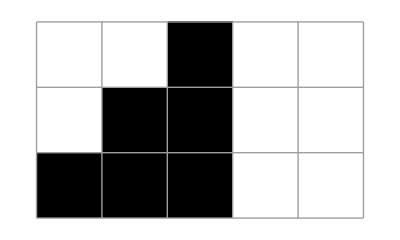

```mathematica
ArrayPlot[CellularAutomaton[110,{0,0,1,0,0},2],Mesh->True]
```

```mathematica
ArrayPlot[mycell[{{1,1,1}->0,{1,1,0}->1,{1,0,1}->1,{1,0,0}->0,{0,1,1}->1,{0,1,0}->1,{0,0,1}->1,{0,0,0}->0},{0,0,1,0,0},2],Mesh->True]
```

-Graphics-